```mathematica
ComplexPlot3D[(z-1)/(z+1),{z, -2-I,2+I}]
```

-Graphics3D-

```mathematica
Solve[y==(z-1)/(z+1),z]
```

{{z→(-1-y)/(-1+y)}}

```mathematica
Clear[CC];
CC=MatrixSymbol["CC",{3,3}];
Id=IdentityMatrix[3];

ccSol=NDSolveValue[{CC'[t]==(Id-CC[t]).df[y[t]].(Id+CC[t])/2,CC[0]==ConstantArray[0,{3,3}]},CC,{t,0,tmax}];

ccSol[0.5]//MatrixForm
```

```mathematica
Ross[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x+a y,b+z (x-c)}
dRoss[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z,0,x-c}}
p={0.12,0.2,2.8};  y0={1,2,3}; TMax=123;
f=Ross[p];df=dRoss[p];
Id=IdentityMatrix[3];
y=VectorSymbol["y",3];
J=MatrixSymbol["J",{3,3}];
CC=MatrixSymbol["CC",{3,3}]
```

MatrixSymbol[CC,{3,3}]

```mathematica
$VersionNumber
```

13.3

NDSolveValue::ndfdmc: Computed derivatives do not have dimensionality consistent with the initial conditions.

Set::shape: Lists {ySol,JSol,MSol} and … are not the same shape.

NDSolveValue[{VectorSymbol[y,3]'[t]==Ross[{0.12,0.2,2.8}][VectorSymbol[y,3][t]],VectorSymbol[y,3][0]=={1,2,3},MatrixSymbol[J,{3,3}]'[t]==dRoss[{0.12,0.2,2.8}][VectorSymbol[y,3][t]].MatrixSymbol[J,{3,3}][t],MatrixSymbol[J,{3,3}][0]=={{1,0,0},{0,1,0},{0,0,1}},MatrixSymbol[CC,{3,3}]'[t]==0.5 {{1-MatrixSymbol[CC,{3,3}][t],-MatrixSymbol[CC,{3,3}][t],-MatrixSymbol[CC,{3,3}][t]},{-MatrixSymbol[CC,{3,3}][t],1-MatrixSymbol[CC,{3,3}][t],-MatrixSymbol[CC,{3,3}][t]},{-MatrixSymbol[CC,{3,3}][t],-MatrixSymbol[CC,{3,3}][t],1-MatrixSymbol[CC,{3,3}][t]}}.dRoss[{0.12,0.2,2.8}][VectorSymbol[y,3][t]].{{1+MatrixSymbol[CC,{3,3}][t],MatrixSymbol[CC,{3,3}][t],MatrixSymbol[CC,{3,3}][t]},{MatrixSymbol[CC,{3,3}][t],1+MatrixSymbol[CC,{3,3}][t],MatrixSymbol[CC,{3,3}][t]},{MatrixSymbol[CC,{3,3}][t],MatrixSymbol[CC,{3,3}][t],1+MatrixSymbol[CC,{3,3}][t]}},MatrixSymbol[CC,{3,3}][0]=={{0,0,0},{0,0,0},{0,0,0}}},{VectorSymbol[y,3],MatrixSymbol[J,{3,3}],MatrixSymbol[CC,{3,3}]},{t,0,123}]

-Graphics3D-

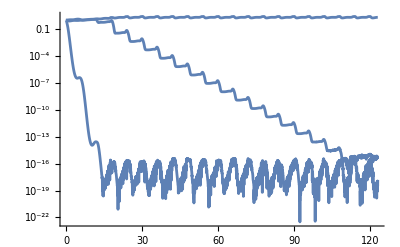

```mathematica
{ySol, JSol,MSol}=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0, 
J'[t]==df[y[t]].J[t],J[0]==Id,
CC'[t]==0.5(Id-CC[t]).df[y[t]].(Id+CC[t]), CC[0]==0*Id},
{y,J,CC},{t,0, TMax}]
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
LogPlot[SingularValueList[JSol[t],Tolerance->0],{t,0,TMax}]
```